```mathematica
SetDirectory@NotebookDirectory[];
<<Notation`
Symbolize[ParsedBoxWrapper[SubscriptBox["_","_"]]]
Symbolize[ParsedBoxWrapper[OverscriptBox["_","_"]]]
```

### Global definitions

```mathematica
(* Potentials *)
Δ[r_]:=r^2-2M r+a^2
Rint[r_]:=(r^2+a^2-a λ)^2-Δ[r](η+(λ-a)^2)
Θint[θ_]:=η+a^2 Cos[θ]^2-λ^2 Cot[θ]^2
(* Radial roots *)
cbrt[x_]:=If[x∈Reals,CubeRoot[x],x^(1/3)]
Â=a^2-η-λ^2;B̂=2 M (η+(λ-a)^2);Ĉ=-a^2 η;
P=-(Â)^2/12-Ĉ;Q=-(Â)/3(((Â)/6)^2-Ĉ)-(B̂)^2/8;Subscript[Δ, 3]=-2^2 P^3-3^3 Q^2;
Subscript[ξ, 0]=cbrt[-Q/2+√(-Subscript[Δ, 3]/108)]+cbrt[-Q/2-√(-Subscript[Δ, 3]/108)]-(Â)/3;z=√(Subscript[ξ, 0]/2);
Subscript[R̂, 1]=-z-√(-(Â)/2-z^2+(B̂)/(4z));Subscript[R̂, 2]=-z+√(-(Â)/2-z^2+(B̂)/(4z));Subscript[R̂, 3]=z-√(-(Â)/2-z^2-(B̂)/(4z));Subscript[R̂, 4]=z+√(-(Â)/2-z^2-(B̂)/(4z));
(* Polar roots *)
SubPlus[u]=Subscript[Δ, θ]+√(Subscript[Δ, θ]^2+η/a^2);SubMinus[u]=Subscript[Δ, θ]-√(Subscript[Δ, θ]^2+η/a^2);Subscript[Δ, θ]=1/2(1-(η+λ^2)/a^2);
(* Toroidal coordinates *)
Subscript[ϕ, o][τ_]:=Subscript[J, ϕ][τ]+λ Subscript[G, ϕ][τ]
Subscript[t, o][τ_]:=Subscript[J, t][τ]+a^2 Subscript[G, t][τ]
Subscript[J, ϕ][τ_]:=(2M a)/(SubPlus[r]-SubMinus[r])((SubPlus[r]-(a λ)/(2M))SubPlus[J][τ]-(SubMinus[r]-(a λ)/(2M))SubMinus[J][τ])
Subscript[J, t][τ_]:=(2M)^2/(SubPlus[r]-SubMinus[r])(SubPlus[r](SubPlus[r]-(a λ)/(2M))SubPlus[J][τ]-SubMinus[r](SubMinus[r]-(a λ)/(2M))SubMinus[J][τ])+(2M)^2 τ+2M Subscript[J, 1][τ]+Subscript[J, 2][τ]
(* Additional quantities *)
SubPlus[r]=M+√(M^2-a^2);SubMinus[r]=M-√(M^2-a^2);
Subscript[r, 21]=Subscript[r, 2]-Subscript[r, 1];Subscript[r, 31]=Subscript[r, 3]-Subscript[r, 1];Subscript[r, 32]=Subscript[r, 3]-Subscript[r, 2];Subscript[r, 41]=Subscript[r, 4]-Subscript[r, 1];Subscript[r, 42]=Subscript[r, 4]-Subscript[r, 2];Subscript[r, 43]=Subscript[r, 4]-Subscript[r, 3];
Subscript[r, +1]=SubPlus[r]-Subscript[r, 1];Subscript[r, +2]=SubPlus[r]-Subscript[r, 2];Subscript[r, +3]=SubPlus[r]-Subscript[r, 3];Subscript[r, +4]=SubPlus[r]-Subscript[r, 4];
Subscript[r, -1]=SubMinus[r]-Subscript[r, 1];Subscript[r, -2]=SubMinus[r]-Subscript[r, 2];Subscript[r, -3]=SubMinus[r]-Subscript[r, 3];Subscript[r, -4]=SubMinus[r]-Subscript[r, 4];
EllipticEPrime[ϕ_,m_]:=(EllipticE[ϕ,m]-EllipticF[ϕ,m])/(2 m)
EllipticEPrime[ϕ,m]==D[EllipticE[ϕ,m], m]
```

True

#### Bug fix for EllipticPi[n,ϕ,m] when n>1

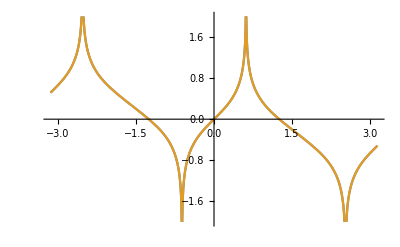

```mathematica
EllipticPiFix[N_,ϕ_,m_]:=EllipticF[ϕ,m]-EllipticPi[m/N,ϕ,m]+1/(2 √((N-1)(1-m/N)))Log[Abs[(√((N-1)(1-m/N)) Tan[ϕ]+√(1-m Sin[ϕ]^2))/(√(1-m Sin[ϕ]^2)-√((N-1)(1-m/N)) Tan[ϕ])]]/;(N>1&&-π<ϕ<π&&0<m<1)
EllipticPiFix[N_,ϕ_,m_]:=EllipticPi[N,ϕ,m]/;(0<N<1&&-π<ϕ<π&&0<m<1)
Block[{n=3,m=0.6},
Plot[{EllipticPiFix[n,ϕ,m],EllipticPi[n,ϕ,m]},{ϕ,-π,π},GridLines->{{ArcSin[1/(√n)],π-ArcSin[1/(√n)]},{}},PlotRange->{-2,2}]]
```

#### Other elliptic integrals

```mathematica
Subscript[R, 1][α_,φ_,j_]:=1/(1-α^2)(EllipticPiFix[α^2/(α^2-1),φ,j]-α/2 √((α^2-1)/(j+(1-j)α^2))Log[Abs[(√((α^2-1)/(j+(1-j)α^2))√(1-j Sin[φ]^2)+Sin[φ])/(√((α^2-1)/(j+(1-j)α^2))√(1-j Sin[φ]^2)-Sin[φ])]])
Subscript[R, 2][α_,φ_,j_]:=1/(α^2-1)(EllipticF[φ,j]-α^2/(j+(1-j)α^2) (EllipticE[φ,j]-(α Sin[φ] √(1-j Sin[φ]^2))/(1+α Cos[φ]))) +1/(j+(1-j)α^2)(2j-α^2/(α^2-1))Subscript[R, 1][α,φ,j]
Subscript[S, 1][α_,φ_,j_]:=1/(1+α^2)(EllipticF[φ,j]+α^2 EllipticPiFix[1+α^2,φ,j]-α/2 √((α^2+1)/(1-j+α^2))Log[Abs[(1-√((α^2+1)/(1-j+α^2)))/(1+√((α^2+1)/(1-j+α^2)))(1+√((α^2+1)/(1-j+α^2))√(1-j Sin[φ]^2))/(1-√((α^2+1)/(1-j+α^2))√(1-j Sin[φ]^2))]])
Subscript[S, 2][α_,φ_,j_]:=-1/((1+α^2)(1-j+α^2))((1-j) EllipticF[φ,j]+α^2 EllipticE[φ,j]+(α^2 √(1-j Sin[φ]^2) (α-Tan[φ]))/(1+α Tan[φ])-α^3)+(1/(1+α^2)+(1-j)/(1-j+α^2))Subscript[S, 1][α,φ,j]
```

```mathematica
Clear[x]
```

### Numerics

#### Analytics

```mathematica
τmax1[ai_,rs_,νr_,r1_,r2_,r3_,r4_]:=Block[{a=ai,M=1,Subscript[r, s]=rs,Subscript[ν, r]=νr,Subscript[r, 1]=r1,Subscript[r, 2]=r2,Subscript[r, 3]=r3,Subscript[r, 4]=r4,k,Subscript[J, 0]},
k=(Subscript[r, 32] Subscript[r, 41])/(Subscript[r, 31] Subscript[r, 42]);
Subscript[J, 0][r_]:=2/(√(Subscript[r, 31] Subscript[r, 42]))EllipticF[ArcSin[√((r-Subscript[r, 2])/(r-Subscript[r, 1])Subscript[r, 31]/Subscript[r, 32])],k];
Subscript[J, 0][Subscript[r, s]]-Subscript[J, 0][SubPlus[r]]+If[Subscript[ν, r]==1,2(Subscript[J, 0][Subscript[r, 3]]-Subscript[J, 0][Subscript[r, s]]),0]
]
τmax2[ai_,rs_,νr_,r1_,r2_,r3_,r4_]:=Block[{a=ai,M=1,Subscript[r, s]=rs,Subscript[ν, r]=νr,Subscript[r, 1]=r1,Subscript[r, 2]=r2,Subscript[r, 3]=r3,Subscript[r, 4]=r4,k,Subscript[J, 0],Subscript[J, max]},
k=(Subscript[r, 32] Subscript[r, 41])/(Subscript[r, 31] Subscript[r, 42]);
Subscript[J, 0][r_]:=2/(√(Subscript[r, 31] Subscript[r, 42]))EllipticF[ArcSin[√((r-Subscript[r, 4])/(r-Subscript[r, 3])Subscript[r, 31]/Subscript[r, 41])],k];
Subscript[J, max]=2/(√(Subscript[r, 31] Subscript[r, 42]))EllipticF[ArcSin[√(Subscript[r, 31]/Subscript[r, 41])],k];
If[Subscript[ν, r]==1,Subscript[J, max]-Subscript[J, 0][Subscript[r, s]],
If[Subscript[r, 4]<SubPlus[r],Subscript[J, 0][Subscript[r, s]]-Subscript[J, 0][SubPlus[r]],Subscript[J, max]-Subscript[J, 0][Subscript[r, s]]+2(Subscript[J, 0][Subscript[r, s]]-Subscript[J, 0][Subscript[r, 4]])]](*BUG REPLACED Subscript[J, max]-Subscript[J, 0][Subscript[r, s]]+If[Subscript[ν, r]==-1,2(Subscript[J, 0][Subscript[r, s]]-Subscript[J, 0][Subscript[r, 4]]),0]*)
]
τmax3[ai_,rs_,νr_,r1_,r2_,r3_,r4_]:=Block[{a=ai,M=1,Subscript[r, s]=rs,Subscript[ν, r]=νr,Subscript[r, 1]=r1,Subscript[r, 2]=r2,Subscript[r, 3]=r3,Subscript[r, 4]=r4,Ã,B̃,Subscript[k, 3],Subscript[J, 0],Subscript[J, max]},
Ã=√(Subscript[r, 32] Subscript[r, 42])//Chop;B̃=√(Subscript[r, 31] Subscript[r, 41])//Chop;
Subscript[k, 3]=((Ã+B̃)^2-Subscript[r, 21]^2)/(4 Ã B̃);
Subscript[J, 0][r_]:=1/(√(Ã B̃))EllipticF[ArcCos[(Ã(r-Subscript[r, 1])-B̃(r-Subscript[r, 2]))/(Ã(r-Subscript[r, 1])+B̃(r-Subscript[r, 2]))],Subscript[k, 3]];
Subscript[J, max]=1/(√(Ã B̃))EllipticF[ArcCos[(Ã-B̃)/(Ã+B̃)],Subscript[k, 3]];
If[Subscript[ν, r]==1,Subscript[J, max]-Subscript[J, 0][Subscript[r, s]],Subscript[J, 0][Subscript[r, s]]-Subscript[J, 0][SubPlus[r]]]
]
τmax4[ai_,rs_,νr_,r1_,r2_,r3_,r4_]:=Block[{a=ai,M=1,Subscript[r, s]=rs,Subscript[ν, r]=νr,Subscript[r, 1]=r1,Subscript[r, 2]=r2,Subscript[r, 3]=r3,Subscript[r, 4]=r4,C̃,D̃,Subscript[a, 2],Subscript[b, 1],Subscript[k, 4],Subscript[g, 0],Subscript[J, 0],Subscript[J, max]},
C̃=√(Subscript[r, 31] Subscript[r, 42])//Chop;D̃=√(Subscript[r, 32] Subscript[r, 41])//Chop;Subscript[a, 2]=√(-Subscript[r, 21]^2/4)//Chop;Subscript[b, 1]=(Subscript[r, 3]+Subscript[r, 4])/2//Chop;
Subscript[k, 4]=(4 C̃ D̃)/(C̃+D̃)^2;Subscript[g, 0]=√((4 Subscript[a, 2]^2-(C̃-D̃)^2)/((C̃+D̃)^2-4 Subscript[a, 2]^2));
Subscript[J, 0][r_]:=2/(C̃+D̃)EllipticF[ArcTan[(r+Subscript[b, 1])/Subscript[a, 2]]+ArcTan[Subscript[g, 0]],Subscript[k, 4]];
Subscript[J, max]=2/(C̃+D̃)EllipticF[π/2+ArcTan[Subscript[g, 0]],Subscript[k, 4]];
If[Subscript[ν, r]==1,Subscript[J, max]-Subscript[J, 0][Subscript[r, s]],Subscript[J, 0][Subscript[r, s]]-Subscript[J, 0][SubPlus[r]]]
]
```

#### Numerical integration

```mathematica
Clear[NRay]
NRay[ai_,λi_,ηi_,rs_,θs_,νr_,νθ_]:=Block[{a=ai,M=1,λ=λi,η=ηi,Subscript[r, s]=rs,Subscript[θ, s]=θs,Subscript[ν, r]=νr,Subscript[ν, θ]=νθ,Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4],Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3],Subscript[θ, 4],PolarType,RadialType,Subscript[τ, max],Ψ,Subscript[Ψ, s],Υ,Subscript[Υ, s],Subscript[θ, o],Subscript[G, ϕ],Subscript[G, t]},
(* Compute radial roots and angular turning points numerically *)
{Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4]}={Subscript[R̂, 1],Subscript[R̂, 2],Subscript[R̂, 3],Subscript[R̂, 4]}//Chop;
{Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3],Subscript[θ, 4]}={ArcCos[√SubPlus[u]],ArcCos[√SubMinus[u]],ArcCos[-√SubMinus[u]],ArcCos[-√SubPlus[u]]};
(* Check input parameters are physical and determine motion types *)
(*If[(Abs[λ]≥a&&η≥0)||(Abs[λ]<a&&η>-(Abs[λ]-a)^2),True,Return[Print["Unphysical parameters: change (λ,η)"]]];*)
If[η>0&&Subscript[θ, 1]≤Subscript[θ, s]≤Subscript[θ, 4],PolarType=1,
If[η≤0&&(Subscript[θ, 1]≤Subscript[θ, s]≤Subscript[θ, 2]||Subscript[θ, 3]≤Subscript[θ, s]≤Subscript[θ, 4]),PolarType=0,Return[Print["Unphysical parameters: change θ_s"]]]];
If[Im[Subscript[r, 2]]>0&&SubMinus[r]≤SubPlus[r]≤Subscript[r, s],RadialType=4,
If[Im[Subscript[r, 4]]>0&&Subscript[r, 1]<Subscript[r, 2]<SubMinus[r]≤SubPlus[r]≤Subscript[r, s],RadialType=3,
If[Subscript[r, 1]<Subscript[r, 2]<SubMinus[r]≤SubPlus[r]<Subscript[r, 3]<Subscript[r, 4]≤Subscript[r, s]||Subscript[r, 1]<Subscript[r, 2]<Subscript[r, 3]<Subscript[r, 4]<SubMinus[r]≤SubPlus[r]≤Subscript[r, s],RadialType=2,
If[Subscript[r, 1]<Subscript[r, 2]<SubMinus[r]≤SubPlus[r]≤Subscript[r, s]≤Subscript[r, 3]<Subscript[r, 4],RadialType=1,Return[{Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4]}]]]]];
(* Compute range of Mino time *)
Subscript[τ, max]=If[RadialType==1,τmax1[a,Subscript[r, s],Subscript[ν, r],Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4]],
If[RadialType==2,τmax2[a,Subscript[r, s],Subscript[ν, r],Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4]],
If[RadialType==3,τmax3[a,Subscript[r, s],Subscript[ν, r],Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4]],τmax4[a,Subscript[r, s],Subscript[ν, r],Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4]]]]];
Print["Polar motion is "<>If[PolarType==1,"ordinary","vortical"]<>" and radial motion is type "<>ToString[RadialType]<>" with τ_max="<>ToString[Subscript[τ, max]]];
(* Numerically solve the geodesic equation *)
nray=NDSolve[{r''[τ]==M (η+(a-λ)^2)+(a^2-η-λ^2) r[τ]+2 r[τ]^3,θ''[τ]==(-a^2 Cos[θ[τ]]+λ^2 Cot[θ[τ]] Csc[θ[τ]]^3) Sin[θ[τ]],ϕ'[τ]==a/Δ[r[τ]](r[τ]^2+a^2-a λ)+λ/Sin[θ[τ]]^2-a,t'[τ]==(r[τ]^2+a^2)/Δ[r[τ]](r[τ]^2+a^2-a λ)+a(λ-a Sin[θ[τ]]^2),r[0]==Subscript[r, s],r'[0]==Subscript[ν, r] √Rint[Subscript[r, s]],θ'[0]==Subscript[ν, θ] √Θint[Subscript[θ, s]],θ[0]==Subscript[θ, s],ϕ[0]==0,t[0]==0},{r,θ,ϕ,t},{τ,0,Subscript[τ, max]},WorkingPrecision->30]//Quiet;
nplotr=Plot[r[τ]/.nray,{τ,0,Subscript[τ, max]},PlotStyle->Blue];
nplotθ=Plot[Cos[θ[τ]]/.nray,{τ,0,Subscript[τ, max]},PlotStyle->Blue];
nplotϕ=Plot[ϕ[τ]/.nray,{τ,0,Subscript[τ, max]},PlotStyle->Blue];
nplott=Plot[t[τ]/.nray,{τ,0,Subscript[τ, max]},PlotStyle->Blue];
GraphicsRow[{Show[nplotr],Show[nplotθ],Show[nplotϕ],Show[nplott]},ImageSize->1000]
]/;(-1≤ai≤1&&λi∈Reals&&ηi∈Reals&&1≤rs&&0≤θs≤π&&(νr==1||νr==-1)&&(νθ==1||νθ==-1))
```

#### Simpler integration

```mathematica
Clear[PRay]
(* Solves the geodesic equation for a photon with the given values of conserved quantities η, λ. *)
(* The return value is an inhomogeneous array containing a list of replacements of coordinates to interpolating functions *)
(* , x -> InterpolatingFunction, where the functions are in terms of the coordinate time t, and the last element of *)
(* the list is the max value of the coordinate time t. *)
PRay[ai_,λi_,ηi_,rs_,θs_,νr_,νθ_]:=Block[{a=ai,M=1,λ=λi,η=ηi,Subscript[r, s]=rs,Subscript[θ, s]=θs,Subscript[ν, r]=νr,Subscript[ν, θ]=νθ,Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4],Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3],Subscript[θ, 4],PolarType,RadialType,Subscript[τ, max],Ψ,Subscript[Ψ, s],Υ,Subscript[Υ, s],Subscript[θ, o],Subscript[G, ϕ],Subscript[G, t],τt,Subscript[t, max],nray,parametricPlot},
(* Compute radial roots and angular turning points numerically *)
{Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4]}={Subscript[R̂, 1],Subscript[R̂, 2],Subscript[R̂, 3],Subscript[R̂, 4]}//Chop;
{Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3],Subscript[θ, 4]}={ArcCos[√SubPlus[u]],ArcCos[√SubMinus[u]],ArcCos[-√SubMinus[u]],ArcCos[-√SubPlus[u]]};

Print[StringForm["r1: `1`",Subscript[r, 1]]];
Print[StringForm["r2: `1`",Subscript[r, 2]]];
Print[StringForm["r3: `1`",Subscript[r, 3]]];
Print[StringForm["r4: `1`",Subscript[r, 4]]];

Print[StringForm["r+: `1`",SubPlus[r]]];
Print[StringForm["r-: `1`",SubMinus[r]]];

Print[StringForm["rs: `1`",Subscript[r, s]]];

(* Check input parameters are physical and determine motion types *)
If[η>0&&Subscript[θ, 1]≤Subscript[θ, s]≤Subscript[θ, 4],PolarType=1,
If[η≤0&&(Subscript[θ, 1]≤Subscript[θ, s]≤Subscript[θ, 2]||Subscript[θ, 3]≤Subscript[θ, s]≤Subscript[θ, 4]),PolarType=0,Return[Print["Unphysical parameters: change θ_s"]]]];
If[Im[Subscript[r, 2]]>0&&SubMinus[r]≤SubPlus[r]≤Subscript[r, s],RadialType=4,
If[Im[Subscript[r, 4]]>0&&Subscript[r, 1]<Subscript[r, 2]<SubMinus[r]≤SubPlus[r]≤Subscript[r, s],RadialType=3,
If[Subscript[r, 1]<Subscript[r, 2]<SubMinus[r]≤SubPlus[r]<Subscript[r, 3]<Subscript[r, 4]≤Subscript[r, s]||Subscript[r, 1]<Subscript[r, 2]<Subscript[r, 3]<Subscript[r, 4]<SubMinus[r]≤SubPlus[r]≤Subscript[r, s],RadialType=2,
If[Subscript[r, 1]<Subscript[r, 2]<SubMinus[r]≤SubPlus[r]≤Subscript[r, s]≤Subscript[r, 3]<Subscript[r, 4],RadialType=1,Return[{Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4]}]]]]];

(* Compute range of Mino time *)
Subscript[τ, max]=If[RadialType==1,τmax1[a,Subscript[r, s],Subscript[ν, r],Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4]],
If[RadialType==2,τmax2[a,Subscript[r, s],Subscript[ν, r],Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4]],
If[RadialType==3,τmax3[a,Subscript[r, s],Subscript[ν, r],Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4]],τmax4[a,Subscript[r, s],Subscript[ν, r],Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4]]]]];

(* Numerically solve the geodesic equation *)
nray=NDSolve[{r''[τ]==M (η+(a-λ)^2)+(a^2-η-λ^2) r[τ]+2 r[τ]^3,θ''[τ]==(-a^2 Cos[θ[τ]]+λ^2 Cot[θ[τ]] Csc[θ[τ]]^3) Sin[θ[τ]],ϕ'[τ]==a/Δ[r[τ]](r[τ]^2+a^2-a λ)+λ/Sin[θ[τ]]^2-a,t'[τ]==(r[τ]^2+a^2)/Δ[r[τ]](r[τ]^2+a^2-a λ)+a(λ-a Sin[θ[τ]]^2),r[0]==Subscript[r, s],r'[0]==Subscript[ν, r] √Rint[Subscript[r, s]],θ'[0]==Subscript[ν, θ] √Θint[Subscript[θ, s]],θ[0]==Subscript[θ, s],ϕ[0]==0,t[0]==0},{r,θ,ϕ,t},{τ,0,Subscript[τ, max]},WorkingPrecision->30]//Quiet;

(* Extract τ[t] *)
τt=Cases[Plot[t[τ]/.nray,{τ,0,Subscript[τ, max]}],x_Line:>First@x,Infinity][[1]];
Subscript[t, max]=τt[[-1,2]];
τt=Interpolation[Map[Reverse[#]&,τt]];

Append[Append[Drop[nray[[1]],-1],τ->τt],tmax->Subscript[t, max]]
]/;(-1≤ai≤1&&λi∈Reals&&ηi∈Reals&&1≤rs&&0≤θs≤π&&(νr==1||νr==-1)&&(νθ==1||νθ==-1))

CriticalPRay[ai_,λi_,ηi_,rs_,θs_,νr_,νθ_]:=Block[{a=ai,M=1,λ=λi,η=ηi,Subscript[r, s]=rs,Subscript[θ, s]=θs,Subscript[ν, r]=νr,Subscript[ν, θ]=νθ,Subscript[r, 1],Subscript[r, 2],Subscript[r, 3],Subscript[r, 4],Subscript[θ, 1],Subscript[θ, 2],Subscript[θ, 3],Subscript[θ, 4],PolarType,RadialType,Subscript[τ, max],Ψ,Subscript[Ψ, s],Υ,Subscript[Υ, s],Subscript[θ, o],Subscript[G, ϕ],Subscript[G, t],τt,Subscript[t, max],nray,parametricPlot,Subscript[τ, eff]},
(* Numerically solve the geodesic equation *)
Subscript[τ, max]=5;
nray=NDSolve[{θ''[τ]==(-a^2 Cos[θ[τ]]+λ^2 Cot[θ[τ]] Csc[θ[τ]]^3) Sin[θ[τ]],ϕ'[τ]==a/Δ[Subscript[r, s]](Subscript[r, s]^2+a^2-a λ)+λ/Sin[θ[τ]]^2-a,t'[τ]==(Subscript[r, s]^2+a^2)/Δ[Subscript[r, s]](Subscript[r, s]^2+a^2-a λ)+a(λ-a Sin[θ[τ]]^2),θ'[0]==Subscript[ν, θ] √Θint[Subscript[θ, s]],θ[0]==Subscript[θ, s],ϕ[0]==0,t[0]==0},{θ,ϕ,t},{τ,0,Subscript[τ, max]},WorkingPrecision->30]//Quiet;

plot=Plot[t[τ]/.nray,{τ,0,Subscript[τ, max]}];
Print[plot];
(* Extract τ[t] *)
Subscript[τ, eff]=5;
τt=Cases[Plot[t[τ]/.nray,{τ,0,Subscript[τ, eff]}],x_Line:>First@x,Infinity][[1]];
Subscript[t, max]=τt[[-1,2]];
τt=Interpolation[Map[Reverse[#]&,τt]];
Append[Append[Drop[nray[[1]],-1],τ->τt],tmax->Subscript[t, max]]
]/;(-1≤ai≤1&&λi∈Reals&&ηi∈Reals&&1≤rs&&0≤θs≤π&&(νr==1||νr==-1)&&(νθ==1||νθ==-1))
```

### Ray Tracing

```mathematica
sphericalToCartesian[r_,θ_,ϕ_]:=Module[{x,y,z},
x=r*Sin[θ]*Cos[ϕ];
y=r*Sin[θ]*Sin[ϕ];
z=r*Cos[θ];
{x,y,z}
]

(* The photon sphere radial bounds *)
radialBounds=Block[{M=1,a=94/100},
{SubPlus[r],SubMinus[r]}/.{SubPlus[r]->2 M (1+Cos[2/3 ArcCos[a/M]]),SubMinus[r]->2 M (1+Cos[2/3 ArcCos[-a/M]])}//N
]

(* Obtain the critical values of conserved quantities at a given radius in the photon sphere *)
getληCritical[rcrit_,Mstar_,astar_]:=Module[{},
{λ̃,η̃}/.{λ̃->a+r/a(r-(2Δ[r])/(r-M)),η̃->r^3/a^2((4M Δ[r])/(r-M)^2-r)}/.{M->Mstar,a->astar,r->rcrit}//N
]
```

{3.94637,1.42524}

#### Sub, Super, Critical Rays

```mathematica
(* The values of the conserved quantities η,λ that produce a bound ray at 3M *)
getληCritical[3,1,94/100]

(* Sub, super, and critical rays. Obtained by perturbing about the critical values from the preceding calculation. *)
ray1=PRay[94/100,-1.87999999999999,26.99999999999999,3,90 π/180,1,1];
ray2=PRay[94/100,-1.8799999,26.999999,3,90 π/180,1,1];
ray3=PRay[94/100,-1.89,26.9999,3,90 π/180,1,1];
```

{-1.88,27.}

r1: -6.41333

r2: 0.413327

r3: 3.-2.98023×10^-8 ⅈ

r4: 3.+2.98023×10^-8 ⅈ

r+: 1+(√291)/50

r-: 1-(√291)/50

rs: 3

r1: -6.41333

r2: 0.413327

r3: 3.-0.00039937 ⅈ

r4: 3.+0.00039937 ⅈ

r+: 1+(√291)/50

r-: 1-(√291)/50

rs: 3

r1: -6.41708

r2: 0.412447

r3: 3.001

r4: 3.00363

r+: 1+(√291)/50

r-: 1-(√291)/50

rs: 3

```mathematica
(* Camera's parametric trajectory *)
rCam[t_]:=(1+√(1-(94/100)^2))+5;
θCam[t_]:=π/2;
ϕCam[ω_,t_,ϕ0_]:=(2 π ω*t)+ϕ0;
```

```mathematica
SetDirectory@NotebookDirectory[]

frameRate=40.0; 
tMax=90.0;
Δt=tMax/(frameRate*tMax);
```

/home/trevor/github/kerr-ray-tracing

```mathematica
(* Export the trajectories to csvs for usage in javascript code. *)
(* We scale units by 10 for convenience in javascript code. *)
10*Table[{r[τ[s]]Sin[θ[τ[s]]]Cos[ϕ[τ[s]]],r[τ[s]]Sin[θ[τ[s]]]Sin[ϕ[τ[s]]],r[τ[s]]Cos[θ[τ[s]]]}/.ray1,{s,0,tMax,Δt}];
Export["./trajectories/subsupercritical/ray1.csv",%]

10*Table[{r[τ[s]]Sin[θ[τ[s]]]Cos[ϕ[τ[s]]],r[τ[s]]Sin[θ[τ[s]]]Sin[ϕ[τ[s]]],r[τ[s]]Cos[θ[τ[s]]]}/.ray2,{s,0,tMax,Δt}];
Export["./trajectories/subsupercritical/ray2.csv",%]

10*Table[{r[τ[s]]Sin[θ[τ[s]]]Cos[ϕ[τ[s]]],r[τ[s]]Sin[θ[τ[s]]]Sin[ϕ[τ[s]]],r[τ[s]]Cos[θ[τ[s]]]}/.ray3,{s,0,tMax,Δt}];
Export["./trajectories/subsupercritical/ray3.csv",%]

10*Table[sphericalToCartesian[rCam[t],θCam[t],ϕCam[1/240,t,π/2]]//N,{t,0,tMax,Δt}];
Export["./trajectories/subsupercritical/cameraTrajectory.csv",%]
```

```mathematica
(* Animate the trajectories along with the black hole. *)
colortable={Blue,Red,Green};
Manipulate[
Show[
Graphics3D[{Black,Sphere[{0,0,0},10*(1+√(1-(94/100)^2))]}],
ParametricPlot3D[10*{r[τ[s]]Sin[θ[τ[s]]]Cos[ϕ[τ[s]]],r[τ[s]]Sin[θ[τ[s]]]Sin[ϕ[τ[s]]],r[τ[s]]Cos[θ[τ[s]]]}/.ray1,{s,0,i},PlotStyle->colortable[[1]]],
ParametricPlot3D[10*{r[τ[s]]Sin[θ[τ[s]]]Cos[ϕ[τ[s]]],r[τ[s]]Sin[θ[τ[s]]]Sin[ϕ[τ[s]]],r[τ[s]]Cos[θ[τ[s]]]}/.ray2,{s,0,i},PlotStyle->colortable[[2]]],
ParametricPlot3D[10*{r[τ[s]]Sin[θ[τ[s]]]Cos[ϕ[τ[s]]],r[τ[s]]Sin[θ[τ[s]]]Sin[ϕ[τ[s]]],r[τ[s]]Cos[θ[τ[s]]]}/.ray3,{s,0,i},PlotStyle->colortable[[3]]],
ParametricPlot3D[10*sphericalToCartesian[rCam[t],θCam[t],ϕCam[1/240,t,π/2]],{t,0,i}],
PlotRange->100{{-1,1},{-1,1},{-1,1}}
],
{i,1,tMax}]
```

InterpolatingFunction::dmval: Input value {23.0891} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {23.0891} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

#### Pairwise Trajectories to Demonstrate the Effect of the Lyapunov Exponent

```mathematica
(* The Lyapunov exponent *)
γ[astar_,Mstar_,r_]:=Module[{uplus,uminus,integrand},
uplus=r/(a^2(r-M)^2)(-r^3+3 M^2 r-2 a^2 M+2 √(M Δ[r](2 r^3-3 M r^2+a^2 M)));
uminus=r/(a^2(r-M)^2)(-r^3+3 M^2 r-2 a^2 M-2 √(M Δ[r](2 r^3-3 M r^2+a^2 M)));
integrand=1/(√((1-t^2)(uplus t^2-uminus)))/.{M->Mstar,a->astar};
4/a √(r^2-(M r Δ[r])/(r-M)^2)NIntegrate[integrand,{t,0,1}]/.{M->Mstar,a->astar}
]
```

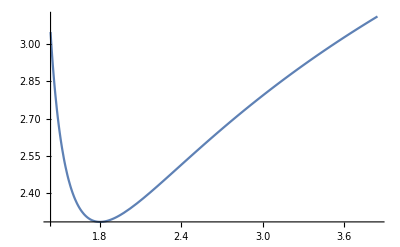

```mathematica
(* The Lyapunov exponent as one traverses the photon sphere *)
Plot[γ[94/100,1,r],{r,Min[radialBounds]+0.01,Max[radialBounds]-0.1}]
```

```mathematica
FindMinimum[γ[94/100,1,r],{r,2.0}];
rMin=r/.%[[2]]; (* The r value which minimizes the Lyapunov. *)

offset=0.5;
numRadii=3;
lower=Min[radialBounds]+0.01;
upper=rMin; 
 (* Critical radii to use. Selecting by hand from the plot above to maximize the effect. *)
rVals=Array[#&,numRadii,{lower,upper}]
lyapunovs=Table[γ[94/100,1,r],{r,rVals}]

raysPerRadius=2;

(* Perturbations off of criticality *)
δs={0.0000001,0.0000001}; 

(* The lyapunov is the exonent which controls how this grows *)
δr=0.01;

σ={{-1,-1},{-1,-1},{-1,-1}}; (* whether to shift up or down depends on radius *)
rays=Table[PRay[94/100,
getληCritical[rVals[[i]],1,94/100][[1]]+σ[[i,1]]δs[[j]],
getληCritical[rVals[[i]],1,94/100][[2]]+σ[[i,2]]δs[[j]],
rVals[[i]]+j,2*δr,90 π/180,1,1
],{i,1,numRadii},{j,1,raysPerRadius}];
```

```mathematica
(* Camera trajectory *)
rCam[t_]:=(1+√(1-(94/100)^2))+3;
θCam[t_]:=π/2-π/8;
ϕCam[ω_,t_,ϕ0_]:=(2 π ω*t)+ϕ0;

δt=0.5;
ωstar=1/360;
ϕ0star=-π/6;
Manipulate[
Show[
Table[
ParametricPlot3D[sphericalToCartesian[r[τ[s]],θ[τ[s]],ϕ[τ[s]]]/.rays[[i,j]],{s,0,k*δt}],
{i,1,numRadii},{j,1,raysPerRadius}
],
ParametricPlot3D[sphericalToCartesian[rCam[t],θCam[t],ϕCam[ωstar,t,ϕ0star]],{t,0,k*δt}],
Graphics3D[{Black,Sphere[{0,0,0},(1+√(1-(94/100)^2))]}],
PlotRange->9{{-1,1},{-1,1},{-1,1}}
],
{k,1,50}]
```

Table::iterb: Iterator {i,1,numRadii} does not have appropriate bounds.

ParametricPlot3D::plln: Limiting value 35.6 δt in {t,0,35.6 δt} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Table[ParametricPlot3D[sphericalToCartesian[r[τ[s]],θ[τ[s]],ϕ[τ[s]]]/.rays⟦i,j⟧,{s,0,FE`k$$287 δt}],{i,1,numRadii},{j,1,raysPerRadius}],ParametricPlot3D[sphericalToCartesian[rCam[t],θCam[t],ϕCam[ωstar,t,ϕ0star]],{t,0,FE`k$$287 δt}],,PlotRange→{{-9,9},{-9,9},{-9,9}}].

Table::iterb: Iterator {i,1,numRadii} does not have appropriate bounds.

ParametricPlot3D::plln: Limiting value 35.6 δt in {t,0,35.6 δt} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Table[ParametricPlot3D[sphericalToCartesian[r[τ[s]],θ[τ[s]],ϕ[τ[s]]]/.rays⟦i,j⟧,{s,0,FE`k$$287 δt}],{i,1,numRadii},{j,1,raysPerRadius}],ParametricPlot3D[sphericalToCartesian[rCam[t],θCam[t],ϕCam[ωstar,t,ϕ0star]],{t,0,FE`k$$287 δt}],,PlotRange→{{-9,9},{-9,9},{-9,9}}].

```mathematica
SetDirectory@NotebookDirectory[]
frameRate=60.0; 
tMax=60.0;
Δt=tMax/(frameRate*tMax);
baseName="./trajectories/pairwise/ray";
docType=".csv";
Do[
Export[
StringJoin[baseName,ToString[(i-1)*raysPerRadius+j],docType],
Table[10*sphericalToCartesian[r[τ[s]],θ[τ[s]],ϕ[τ[s]]]/.rays[[i,j]],{s,0,tMax,Δt}]
]
,{i,1,numRadii},{j,1,raysPerRadius}]

10*Table[sphericalToCartesian[rCam[t],θCam[t],ϕCam[ωstar,t,ϕ0star]]//N,{t,0,tMax,Δt}];
Export["./trajectories/pairwise/cameraTrajectory.csv",%]
```

/home/trevor/github/kerr-ray-tracing

./trajectories/pairwise/cameraTrajectory.csv

{{tmax→139.953,tmax→63.2944},{tmax→130.661,tmax→68.0293},{tmax→120.698,tmax→66.7638}}

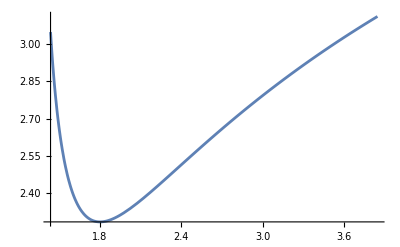

```mathematica
Table[rays[[i,j]][[5]],{i,1,numRadii},{j,1,raysPerRadius}]
```

```mathematica
<<MaTeX`
```

Get::noopen: Cannot open MaTeX`.

$Failed

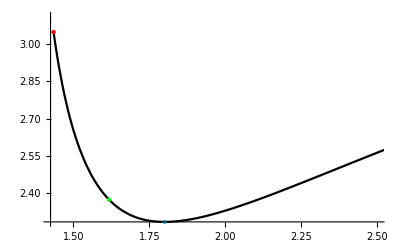

```mathematica
colors={RGBColor[1,0,0], RGBColor[0,1,0], RGBColor["#48B8D0"]};
plot=Show[
Plot[γ[94/100,1,r],{r,Min[radialBounds]+0.01,Max[radialBounds]-0.1},
PlotRange->{{Min[radialBounds],2.5},All},PlotStyle->Black],
ListPlot[Table[Style[{rVals[[i]],γ[94/100,1,rVals[[i]]]},colors[[i]] ],{i,1,Length[rVals]}], 
PlotStyle->PointSize[Large]],
AxesLabel->{
Style["",FontSize->14,FontColor->Black],
Style["",FontSize->14,FontColor->Black]
}
]
```

```mathematica
SetDirectory@NotebookDirectory[];
Export["./movies/for-peter.png",plot,ImageResolution->300]
```

./movies/for-peter.png

#### New Animation

```mathematica
linSpace[a_,b_,n_]:=Table[a+(b-a)*(i-1)/(n-1),{i,1,n}]
```

```mathematica
rcrit=SetPrecision[2.192,100];
astar=680/1000;
Mstar=1;
{λcrit,ηcrit}=getληCritical[rcrit,Mstar,astar]
```

{2.96875,6.70918}

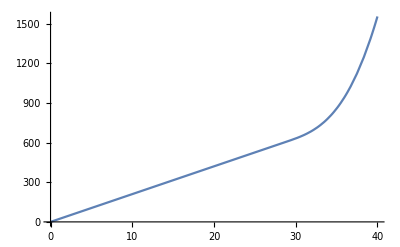

```mathematica
ray1=CriticalPRay[astar,λcrit,ηcrit,rcrit,90 π/180,1,-1];
```

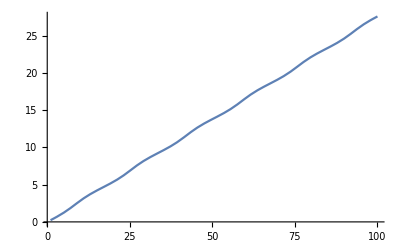

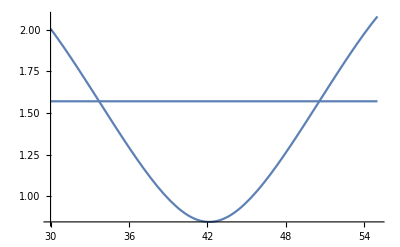

```mathematica
Plot[ϕ[τ[t]]/.ray1,{t,1,100}]
Plot[{θ[τ[t]],π/2}/.ray1,{t,30,55}]
```

```mathematica
(* Camera's parametric trajectory *)
(* Camera trajectory *)
rCam[t_]:=(1+√(1-(94/100)^2))+5;
θCam[t_]:=π/3;
ϕCam[ω_,t_,ϕ0_]:=(2 π ω*(t-33))+ϕ0;
```

```mathematica
Manipulate[
Show[
Graphics3D[{Black,Sphere[{0,0,0},10*(1+√(1-(94/100)^2))]}],
ParametricPlot3D[10*{rcrit Sin[θ[τ[s]]]Cos[ϕ[τ[s]]],rcrit Sin[θ[τ[s]]]Sin[ϕ[τ[s]]],rcrit Cos[θ[τ[s]]]}/.ray1,{s,0,i},PlotStyle->Green],
ParametricPlot3D[10*sphericalToCartesian[rCam[t],θCam[t],ϕCam[-1/70,t,-π]],{t,32,i}],
PlotRange->100{{-1,1},{-1,1},{-1,1}}
],
{i,1,600,1}]
```

ReplaceAll::reps: {ray1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {109.482} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3.78931} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {109.482} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

ReplaceAll::reps: {ray1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {ray1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
SetDirectory@NotebookDirectory[]

frameRate=25.0; 
tMax=600.;
Δt=1/frameRate;

numIter=Floor[tMax/Δt];
tVals=Table[tMax*((i-1)/(numIter-1)),{i,1,numIter}];

(* The fully traced trajectory *)
10*Table[{rcrit Sin[θ[τ[s]]]Cos[ϕ[τ[s]]],rcrit Sin[θ[τ[s]]]Sin[ϕ[τ[s]]],rcrit Cos[θ[τ[s]]]}/.ray1,{s,tVals}];
Export["./trajectories/tau/ray1FullyTraced.csv",%]
```

/home/trevor/github/kerr-ray-tracing

./trajectories/tau/ray1FullyTraced.csv

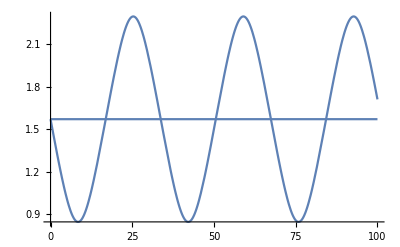

```mathematica
Plot[{θ[τ[t]],π/2}/.ray1,{t,0,100}]
```

```mathematica
crossingTimes={};

f[t_]:=θ[τ[t]]/.ray1;
crossingTimeSpacing=16.0;
numberOfSegments=6;
base=35;

crossingTimes=Table[t/.FindRoot[f[t]-π/2,{t,base+i*crossingTimeSpacing}],{i,0,numberOfSegments}]

Table[linSpace[crossingTimes[[i]],crossingTimes[[i+1]],Floor[(crossingTimes[[i+1]]-crossingTimes[[i]])/Δt]] ,{i,1,Length[crossingTimes]-1}];
Flatten[%];
tVals=DeleteDuplicates[%];

Table[crossingTimes[[i]]-crossingTimes[[i-1]],{i,2,Length[crossingTimes]}]

(* The first one isn't a "crossing" in the context of the javascript. *)
crossingTimes=crossingTimes[[2 ;;]]
```

{33.7124,50.5528,67.4148,84.2867,101.138,117.977,134.827}

{16.8403,16.862,16.8719,16.8518,16.8384,16.8498}

{50.5528,67.4148,84.2867,101.138,117.977,134.827}

```mathematica
radialOffset=0;

(* The highlighted section *)
res=Table[{10 rcrit Sin[θ[τ[s]]]Cos[ϕ[τ[s]]],10 rcrit Sin[θ[τ[s]]]Sin[ϕ[τ[s]]],10 rcrit Cos[θ[τ[s]]],s,ϕ[τ[s]],If[MemberQ[crossingTimes,s],1,0]}/.ray1,{s,tVals}];
Export["./trajectories/tau/ray1.csv",%]

(* Projection of the highlighted section and also pushed out further in radius *)
10*Table[{(rcrit+radialOffset) Sin[π/2]Cos[ϕ[τ[s]]],(rcrit+radialOffset) Sin[π/2]Sin[ϕ[τ[s]]],(rcrit+radialOffset) Cos[π/2]}/.ray1,{s,tVals}];
Export["./trajectories/tau/ray1projection.csv",%]

(* Camera trajectory *)
10*Table[sphericalToCartesian[rCam[t],θCam[t],ϕCam[-1/70,t,-π]]//N,{t,tVals}];
Export["./trajectories/tau/cameraTrajectory.csv",%]
```

./trajectories/tau/ray1.csv

./trajectories/tau/ray1projection.csv

./trajectories/tau/cameraTrajectory.csv

```mathematica
res[[1;;5]] // MatrixForm
```

(-21.666 | 3.32728 | 1.10766×10^-14 | 33.7124 | 9.2724 | 1
-21.6846 | 3.2034 | 0.0677395 | 33.7375 | 9.27811 | 0
-21.7022 | 3.07939 | 0.135478 | 33.7626 | 9.28383 | 0
-21.7189 | 2.95525 | 0.203213 | 33.7876 | 9.28954 | 0
-21.7347 | 2.83098 | 0.270944 | 33.8127 | 9.29526 | 0)

#### Sequence of Crossing Times and Azimuthal Displacements

```mathematica
astar=680/1000;
Mstar=1;

rtildeminus=2 * Mstar (1+Cos[2/3 ArcCos[-astar/Mstar]])//N
rtildeplus=2 * Mstar (1+Cos[2/3 ArcCos[astar/Mstar]])//N
```

2.05018

3.70642

```mathematica
Clear[GetCrossingTime]
GetCrossingTime[input_]:=Module[{λcrit,ηcrit,ray,f},
rcrit=SetPrecision[input,100];
{λcrit,ηcrit}=getληCritical[rcrit,Mstar,astar];
ray=CriticalPRay[astar,λcrit,ηcrit,rcrit,90 π/180,1,-1];
f[t_]:=θ[τ[t]]/.ray;
t/.FindRoot[f[t]-π/2,{t,18}]
]
```

```mathematica
crossingTimes=Table[{x,GetCrossingTime[x]},{x,2.2,3.7,0.1}]
```

{{2.2,16.8137},{2.3,16.4004},{2.4,16.1285},{2.5,15.9545},{2.6,15.8517},{2.7,15.8022},{2.8,15.7937},{2.9,15.8175},{3.,15.8673},{3.1,15.9384},{3.2,16.027},{3.3,16.1303},{3.4,16.2457},{3.5,16.3716},{3.6,16.5065},{3.7,16.6492}}

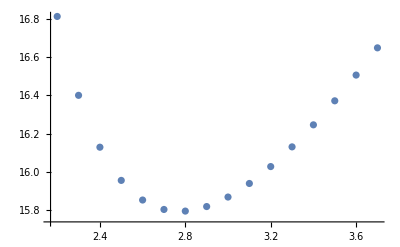

```mathematica
ListPlot[crossingTimes]
```

{2.8,3.2,3.6}

{-0.15451,25.4602}

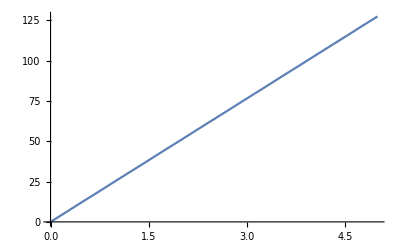

15.7937

{15.7937}

{-2.66717,25.2069}

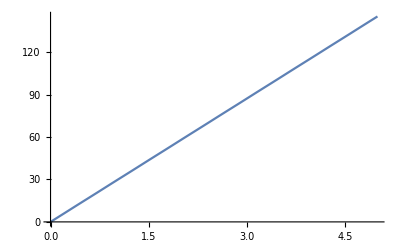

16.027

{15.7937,16.027}

{-5.60127,8.26302}

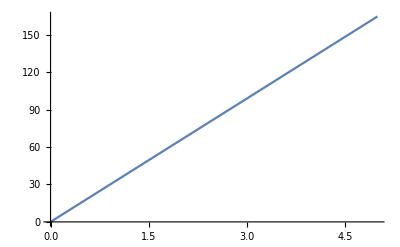

16.5065

{15.7937,16.027,16.5065}

```mathematica
crossingTimesExport={};
{r1,r2,r3}={2.8,3.2,3.6}
rcrit=SetPrecision[r1,100];
{λcrit,ηcrit}=getληCritical[rcrit,Mstar,astar]
ray1=CriticalPRay[astar,λcrit,ηcrit,rcrit,90 π/180,1,-1];
Clear[f]
f[t_]:=θ[τ[t]]/.ray1;
t/.FindRoot[f[t]-π/2,{t,18}]
crossingTimesExport=Append[crossingTimesExport,%]

rcrit=SetPrecision[r2,100];
{λcrit,ηcrit}=getληCritical[rcrit,Mstar,astar]
ray2=CriticalPRay[astar,λcrit,ηcrit,rcrit,90 π/180,1,-1];
Clear[f]
f[t_]:=θ[τ[t]]/.ray2;
t/.FindRoot[f[t]-π/2,{t,18}]
crossingTimesExport=Append[crossingTimesExport,%]

rcrit=SetPrecision[r3,100];
{λcrit,ηcrit}=getληCritical[rcrit,Mstar,astar]
ray3=CriticalPRay[astar,λcrit,ηcrit,rcrit,90 π/180,1,-1];
Clear[f]
f[t_]:=θ[τ[t]]/.ray3;
t/.FindRoot[f[t]-π/2,{t,18}]
crossingTimesExport=Append[crossingTimesExport,%]
```

```mathematica
crossingTimesExpro
```

{60,403}

```mathematica
SetDirectory@NotebookDirectory[]

frameRate=25.0; 
Δt=1/frameRate;

tMax=crossingTimesExport[[1]];

numIter=Floor[tMax/Δt];
tVals=Table[tMax*((i-1)/(numIter-1)),{i,1,numIter}];
10*Table[{r1 Sin[θ[τ[s]]]Cos[ϕ[τ[s]]],r1 Sin[θ[τ[s]]]Sin[ϕ[τ[s]]],r1 Cos[θ[τ[s]]]}/.ray1,{s,tVals}];
Export["./trajectories/sequential-crossing-times/ray1.csv",%]

tMax=crossingTimesExport[[2]];
numIter=Floor[tMax/Δt];
tVals=Table[tMax*((i-1)/(numIter-1)),{i,1,numIter}];
10*Table[{r2 Sin[θ[τ[s]]]Cos[ϕ[τ[s]]],r2 Sin[θ[τ[s]]]Sin[ϕ[τ[s]]],r2 Cos[θ[τ[s]]]}/.ray2,{s,tVals}];
Export["./trajectories/sequential-crossing-times/ray2.csv",%]

tMax=crossingTimesExport[[3]];
numIter=Floor[tMax/Δt];
tVals=Table[tMax*((i-1)/(numIter-1)),{i,1,numIter}];
10*Table[{r3 Sin[θ[τ[s]]]Cos[ϕ[τ[s]]],r3 Sin[θ[τ[s]]]Sin[ϕ[τ[s]]],r3 Cos[θ[τ[s]]]}/.ray3,{s,tVals}];
Export["./trajectories/sequential-crossing-times/ray3.csv",%]
```

/home/trevor/github/kerr-ray-tracing

./trajectories/sequential-crossing-times/ray1.csv

./trajectories/sequential-crossing-times/ray2.csv

./trajectories/sequential-crossing-times/ray3.csv